# Mathematica Code for LOR

## Section 1: The General LOR Frame

Suppose that we want to compute the LOR dynamics for the 5-d vector field:

```mathematica
f[{x1_,x2_,x3_,x4_,x5_},{λ1_,λ2_}]:={x2-x1,x3-x2,x4-x3,x5-x4,x1-x5}+λ1{-x1,-x2,-x3,-x4,-x5}+λ2{x1^2,x2^2,x3^2,x4^2,x5^2};
Manipulate[StreamPlot[Take[f[{x1,x2,0,0,0},{λ1,λ2}],{1,2}],{x1,-10,10},{x2,-10,10}],{λ1,0,1},{λ2,0,1}]
```

Note that the vector field has been defined using the following structure:
					vector_field_name[{var1,var2, . . . , varN}, {par1,par2, . . . ,parK}]
where the variables are passed to the vector field in the first vector argument, and the parameters of the vector field are passed as the second vector variable.

Suppose that we are interested in studying the dynamics near the chart:

```mathematica
σ[{η1_,η2_,η3_},{λ1_,λ2_}]:={η1,η2,η3, λ1*η1^2-η2^2, λ2(η1+η2+η3)}
```

Note that this chart definition follows the same variable/parameter convention as the vector field. We will begin by computing the first fundamental form.

```mathematica
FFF[vars_,pars_][man_]:=Module[{dumvars},
dumvars=Table[Subscript[𝒹,i],{i,1,Length[vars]}];
Transpose[D[man[dumvars,pars],{dumvars}]].D[man[dumvars,pars],{dumvars}]/.Table[dumvars[[i]]->vars[[i]],{i,1,Length[vars]}]]
```

We are leveraging several useful, symbolic properties of Mathematica here; we are taking vector derivatives of our chart with respect to dummy variables (this avoids complications during evaluation) then substituting those variables back for the original variables:

```mathematica
MatrixForm[FFF[{η1,η2,η3},{λ1,λ2}][σ]]
```

(1+4 η1^2 λ1^2+λ2^2 | -4 η1 η2 λ1+λ2^2 | λ2^2
-4 η1 η2 λ1+λ2^2 | 1+4 η2^2+λ2^2 | λ2^2
λ2^2 | λ2^2 | 1+λ2^2)

As this is a codimension 2 manifold, we will need 2 normal vectors for the LOR approach. Some ingenuity can be required to find these.

```mathematica
N1σ[eta_,pars_]:={-pars[[2]],-pars[[2]],-pars[[2]],0,1}/Sqrt[1+3*pars[[2]]^2]
N2σ[{η1_,η2_,η3_},{λ1_,λ2_}]:={(2 η1 λ1+2 η2 λ2^2+4 η1 λ1 λ2^2)/(√(1+3 λ2^2)),
								(-2 η2-4 η2 λ2^2-2 η1 λ1 λ2^2)/(√(1+3 λ2^2)),
								(2 η2 λ2^2-2 η1 λ1 λ2^2)/(√(1+3 λ2^2)),
								(-1-3 λ2^2)/(√(1+3 λ2^2)),
								(-2 η2 λ2+2 η1 λ1 λ2)/(√(1+3 λ2^2))}/
								Sqrt[1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2];
```

This is a normal frame:

```mathematica
MatrixForm[
	FullSimplify[
		Table[{
			N1σ[{η1,η2,η3},{λ1,λ2}].D[σ[{η1,η2,η3},{λ1,λ2}],{var}],
			N2σ[{η1,η2,η3},{λ1,λ2}].D[σ[{η1,η2,η3},{λ1,λ2}],{var}]},
		{var,{η1,η2,η3}}]]]
```

(0 | 0
0 | 0
0 | 0)

We can compute the second fundamental forms

```mathematica
SFF[vars_,pars_][man_,normal_]:=Module[{dumvars},
dumvars=Table[Subscript[𝒹,i],{i,1,Length[vars]}];
Table[normal[vars,pars].D[D[man[dumvars,pars],dumvars[[𝒾]]],dumvars[[𝒿]]],{𝒾,1,Length[vars]},{𝒿,1,Length[vars]}]/.Table[dumvars[[i]]->vars[[i]],{i,1,Length[vars]}]];
```

Here we need to pass the manifold name and the normal vector name:

```mathematica
MatrixForm[SFF[{η1,η2,η3},{λ1,λ2}][σ,N1σ]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
FullSimplify[MatrixForm[SFF[{η1,η2,η3},{λ1,λ2}][σ,N2σ]]]
```

(-(2 λ1 √(1+3 λ2^2))/(√(1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2)) | 0 | 0
0 | (2 √(1+3 λ2^2))/(√(1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2)) | 0
0 | 0 | 0)

Now we can define the tangent exchange operator:

```mathematica
Zip[list1_,list2_]:=If[Length[list1]≠Length[list2],
"List Mismatch",
Sum[list1[[𝓀]]*list2[[𝓀]],{𝓀,1,Length[list1]}]];
TE[vars_,pars_][man_,frame_]:=Module[{tanvars,normvars,dim,codim},
codim=Length[frame];
dim=Length[vars]-codim;
tanvars=Take[vars,{1,dim}];
normvars=Take[vars,{dim+1,dim+codim}];
FFF[tanvars,pars][man]+Zip[normvars,SFF[tanvars,pars][man,#]&/@frame]];
```

We will establish a LOR coordinate convention here, the η variables (the manifold coordinates) will make up the first part of the LOR coordinate vector, and the ξ coordinates will be the second part of the LOR variable coordinate.

```mathematica
FullSimplify[MatrixForm[TE[{η1,η2,η3,ξ1,ξ2},{λ1,λ2}][σ,{N1σ,N2σ}]]]
```

(1+4 η1^2 λ1^2+λ2^2-(2 λ1 √(1+3 λ2^2) ξ2)/(√(1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2)) | -4 η1 η2 λ1+λ2^2 | λ2^2
-4 η1 η2 λ1+λ2^2 | 1+4 η2^2+λ2^2+(2 √(1+3 λ2^2) ξ2)/(√(1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2)) | λ2^2
λ2^2 | λ2^2 | 1+λ2^2)

As promised, the tangent exchange operator is invertible on the patch:

```mathematica
Solve[Det[TE[{η1,η2,η3,0,0},{λ1,λ2}][σ,{N1σ,N2σ}]]==0,Reals]
```

{}

Finally, we can define the Normal Exchange operator

```mathematica
NE[vars_,pars_][man_,frame_]:=Module[{tanvars,dumTanVars,normvars,dim,codim},
codim=Length[frame];
dim=Length[vars]-codim;
tanvars=Take[vars,{1,dim}];
dumTanVars=Table[Subscript[𝒹,i],{i,1,dim}];
normvars=Take[vars,{dim+1,dim+codim}];
Zip[normvars,
	Table[#.D[normVec,{tanvars}],{normVec, #}]&[Table[vec[dumTanVars,pars],{vec,frame}]]
	/.Table[dumTanVars[[𝓀]]->tanvars[[𝓀]],{𝓀,1,dim}]]];
```

The last line is performing a rather complicated process, so we’ll describe it in parts, from right to left.  First, the list of normal vector aliases (named “frame”) is evaluated at a dummy-variable point (dumTanVars) and saved in a list (the Table command does this, using “vec” as a placeholder name for each element of “frame”).  The next Table command is using an anonymous function (like a lambda function in Python), it takes the list its given, computes the derivative of 1 (one) of the elements of the list, then takes the matrix product of that derivative with the original list (here the normal frame). The Table command iterates over the entire list, then the Zip command multiplies the appropriate matrix by some ξ and sums the result.

After all this, we find that this manifold/frame combination has a vanishing normal exchange operator.

```mathematica
MatrixForm[NE[{η1,η2,η3,ξ1,ξ2},{λ1,λ2}][σ,{N1σ,N2σ}]]
```

(0 | 0 | 0
0 | 0 | 0)

The last piece of the LOR dynamics is our LOR coordinate submersion, which we call Ψ.

```mathematica
Ψ[vars_,pars_][man_,frame_]:=Module[{tanVars,normVars,dim,coDim},
coDim=Length[frame];
dim=Length[vars]-coDim;
tanVars=Take[vars,{1,dim}];
normVars=Take[vars,{dim+1,dim+coDim}];
man[tanVars,pars]+Zip[normVars,Table[vec[tanVars,pars],{vec,frame}]]];
```

In action:

```mathematica
FullSimplify[Ψ[{η1,η2,η3,ξ1,ξ2},{λ1,λ2}][σ,{N1σ,N2σ}]]
```

{η1-(λ2 ξ1)/(√(1+3 λ2^2))+(2 (η1 λ1+(η2+2 η1 λ1) λ2^2) ξ2)/(√(1+3 λ2^2) √(1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2)),η2-(λ2 ξ1)/(√(1+3 λ2^2))-(2 (η2+(2 η2+η1 λ1) λ2^2) ξ2)/(√(1+3 λ2^2) √(1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2)),η3+(λ2 (-ξ1+(2 (η2-η1 λ1) λ2 ξ2)/(√(1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2))))/(√(1+3 λ2^2)),-η2^2+η1^2 λ1-(√(1+3 λ2^2) ξ2)/(√(1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2)),(η1+η2+η3) λ2+ξ1/(√(1+3 λ2^2))-(2 (η2-η1 λ1) λ2 ξ2)/(√(1+3 λ2^2) √(1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2))}

#### The LOR Equations

Supposing the above cells have been executed, the following will render the LOR dynamics

```mathematica
LORE[vars_,pars_][man_,frame_,field_]:=Module[{tanvars,dumTanVars,normvars,dim,codim},
codim=Length[frame];
dim=Length[vars]-codim;
tanvars=Take[vars,{1,dim}];
dumTanVars=Table[Subscript[𝒹,i],{i,1,dim}];
normvars=Take[vars,{dim+1,dim+codim}];
Join[#1, Table[vec[tanvars,pars],{vec,frame}].#2-NE[vars,pars][man,frame].#1]&[
			Inverse[TE[vars,pars][man,frame]].(field[Ψ[vars,pars][man,frame],pars].D[man[dumTanVars,pars],{dumTanVars}]),
			field[Ψ[vars,pars][man,frame],pars]]/.Table[dumTanVars[[𝓀]]->tanvars[[𝓀]],{𝓀,1,dim}]];
```

We take a breath, and execute:

```mathematica
LORE[{η1,η2,η3,ξ1,ξ2},{λ1,λ2}][σ,{N1σ,N2σ},f]
```

{1}
 |  |  |  |

While the above is not simple (the manifold we chose is not dynamically relevant, hence there are no simplifications to be made), we should relish the fact that humans need not compute the LOR equations. For convenience, here is all the code needed to compute this transformation in general.  To use do the following:
					1.) Pick a vector field, called “f” below. If you don’t care about parameters, pass {} for the parameter part.
					2.) Pick a chart. Again, if the chart is not parameter dependent, pass {} for the parameter part.
					3.) Define your normal vectors. If you have an n-k dimensional manifold in n-space, you need k orthonormal vectors which are all orthogonal to the Tangent space at every point of patch. The orthonormality condition is crucial.
					4.) Initialize the code below.
					5.) Execute LORE[vars, pars][man, frame, field]

```mathematica
FFF[vars_,pars_][man_]:=Module[{dumvars},
dumvars=Table[Subscript[𝒹,i],{i,1,Length[vars]}];
Transpose[D[man[dumvars,pars],{dumvars}]].D[man[dumvars,pars],{dumvars}]/.Table[dumvars[[i]]->vars[[i]],{i,1,Length[vars]}]];

SFF[vars_,pars_][man_,normal_]:=Module[{dumvars},
dumvars=Table[Subscript[𝒹,i],{i,1,Length[vars]}];
Table[normal[vars,pars].D[D[man[dumvars,pars],dumvars[[𝒾]]],dumvars[[𝒿]]],{𝒾,1,Length[vars]},{𝒿,1,Length[vars]}]/.Table[dumvars[[i]]->vars[[i]],{i,1,Length[vars]}]];

Zip[list1_,list2_]:=If[Length[list1]≠Length[list2],
"List Mismatch",
Sum[list1[[𝓀]]*list2[[𝓀]],{𝓀,1,Length[list1]}]];

TE[vars_,pars_][man_,frame_]:=Module[{tanvars,normvars,dim,codim},
codim=Length[frame];
dim=Length[vars]-codim;
tanvars=Take[vars,{1,dim}];
normvars=Take[vars,{dim+1,dim+codim}];
FFF[tanvars,pars][man]+Zip[normvars,SFF[tanvars,pars][man,#]&/@frame]];

NE[vars_,pars_][man_,frame_]:=Module[{tanvars,dumTanVars,normvars,dim,codim},
codim=Length[frame];
dim=Length[vars]-codim;
tanvars=Take[vars,{1,dim}];
dumTanVars=Table[Subscript[𝒹,i],{i,1,dim}];
normvars=Take[vars,{dim+1,dim+codim}];
Zip[normvars,
	Table[#.D[normVec,{tanvars}],{normVec, #}]&[Table[vec[dumTanVars,pars],{vec,frame}]]
	/.Table[dumTanVars[[𝓀]]->tanvars[[𝓀]],{𝓀,1,dim}]]];
	
Ψ[vars_,pars_][man_,frame_]:=Module[{tanVars,normVars,dim,coDim},
coDim=Length[frame];
dim=Length[vars]-coDim;
tanVars=Take[vars,{1,dim}];
normVars=Take[vars,{dim+1,dim+coDim}];
σ[tanVars,pars]+Zip[normVars,Table[vec[tanVars,pars],{vec,frame}]]];

LORE[vars_,pars_][man_,frame_,field_]:=Module[{tanvars,dumTanVars,normvars,dim,codim},
codim=Length[frame];
dim=Length[vars]-codim;
tanvars=Take[vars,{1,dim}];
dumTanVars=Table[Subscript[𝒹,i],{i,1,dim}];
normvars=Take[vars,{dim+1,dim+codim}];
Join[#1, Table[vec[tanvars,pars],{vec,frame}].#2-NE[vars,pars][man,frame].#1]&[
			Inverse[TE[vars,pars][man,frame]].(field[Ψ[vars,pars][man,frame],pars].D[man[dumTanVars,pars],{dumTanVars}]),
			field[Ψ[vars,pars][man,frame],pars]]/.Table[dumTanVars[[𝓀]]->tanvars[[𝓀]],{𝓀,1,dim}]];
```

```mathematica
f[{x1_,x2_,x3_,x4_,x5_},{λ1_,λ2_}]:={x2-x1,x3-x2,x4-x3,x5-x4,x1-x5}+λ1{-x1,-x2,-x3,-x4,-x5}+λ2{x1^2,x2^2,x3^2,x4^2,x5^2};
σ[{η1_,η2_,η3_},{λ1_,λ2_}]:={η1,η2,η3, λ1*η1^2-η2^2, λ2(η1+η2+η3)};
N1σ[eta_,pars_]:={-pars[[2]],-pars[[2]],-pars[[2]],0,1}/Sqrt[1+3*pars[[2]]^2];
N2σ[{η1_,η2_,η3_},{λ1_,λ2_}]:={(2 η1 λ1+2 η2 λ2^2+4 η1 λ1 λ2^2)/(√(1+3 λ2^2)),
								(-2 η2-4 η2 λ2^2-2 η1 λ1 λ2^2)/(√(1+3 λ2^2)),
								(2 η2 λ2^2-2 η1 λ1 λ2^2)/(√(1+3 λ2^2)),
								(-1-3 λ2^2)/(√(1+3 λ2^2)),
								(-2 η2 λ2+2 η1 λ1 λ2)/(√(1+3 λ2^2))}/
								Sqrt[1+4 η2^2+4 η1^2 λ1^2+(3+8 (η2^2+η1 η2 λ1+η1^2 λ1^2)) λ2^2];
```

```mathematica
LORE[{η1,η2,η3,ξ1,ξ2},{λ1,λ2}][σ,{N1σ,N2σ},f]
```

{1}
 |  |  |  |

### The Frenet LOR Equations

When our base manifold is a Frenet curve, our computations simplify greatly. Suppose we wanted to study the curve:

```mathematica
γ[s_]:={1,s,s^2,s^3,s^4};
```

We can use a build in method for computing the Frenet Frame:

```mathematica
FLORE[vars_,pars_][vec_,basecurve_]:=Module[{w,nw,Nw,κw,list,n,K,Nvec},
w[u_]:=basecurve[u];
nw[u_]:=Sqrt[D[basecurve[ry],ry].D[basecurve[ry],ry]]/.{ry->u};
n=Length[w[u]];
list=FrenetSerretSystem[w[u],u];
κw[p_,i_]:=list[[1]][[i]]/.{u->p};
Nw[p_,i_]:=list[[2]][[i]]/.{u->p};
K[p_]:=If[n==2,0,DiagonalMatrix[Table[κw[p,i],{i,2,n-1}],1]-DiagonalMatrix[Table[κw[p,i],{i,2,n-1}],-1]];
Nvec[vars2_,pars2_]:=Table[vec[w[vars2[[1]]]+Sum[vars2[[i]] Nw[vars2[[1]],i],{i,2,n}],pars2].Nw[vars2[[1]],j],{j,2,n}];
Join[{vec[w[vars[[1]]]+Sum[vars[[i]] Nw[vars[[1]],i],{i,2,n}],pars].Nw[vars[[1]],1]/(nw[vars[[1]]](1-vars[[2]]*κw[vars[[1]],1]))},
Nvec[vars,pars]+(vec[w[vars[[1]]]+Sum[vars[[i]] Nw[vars[[1]],i],{i,2,n}],pars].Nw[vars[[1]],1]/((1-vars[[2]]*κw[vars[[1]],1])))If[n==2,0,K[vars[[1]]].Table[vars[[i]],{i,2,n}]]]];
```

Then:

```mathematica
FLORE[{0,0,0,0,0},{0,0}][f,γ]
```

{0,0,0,1,-1}

## Section 2: LOR and Periodic Orbits

In this section, we will use LOR (specifically the FLORE method) to identify and analyze periodic orbits.  We will use the Goodwin dynamics:

```mathematica
g[{x_,y_,z_},{b_}]:={360/(1.368^12+z^12)-b x, x-.6*y, y - .8 z};
```

We will use a trajectory to construct an admissible simple closed curve.  The trajectory through (1, 1, 1) will work :

```mathematica
traj=NDSolve[{{x'[t],y'[t],z'[t]}==g[{x[t],y[t],z[t]},{1}],{x[0],y[0],z[0]}=={1,1,1}},{x,y,z},{t,0,100}];
ParametricPlot3D[{x[t],y[t],z[t]}/.traj,{t,10,15}]
```

-Graphics3D-

The trajectory is nearly periodic on [10,15], we’ll project the trajectory onto a plane, then fit the (x,y) data to an ellipse.

```mathematica
data=Flatten[Table[{x[t],y[t],z[t]}/.traj,{t,10,15,.1}],1];
A=Table[Append[Take[data[[i]],{1,2}],1],{i,1,Length[data]}];
B=Table[data[[i,3]],{i,1,Length[data]}];
v=Inverse[Transpose[A].A].Transpose[A].B;
```

A is the matrix of (x,y) data, the normal vector for the plane is the pseudo-inverse of A times the vector of z data, called B.

```mathematica
Cost[α1_, α2_, α3_, α4_, α5_] := Sum[(data[[i, 1]]^2 + α1*data[[i, 1]]*data[[i, 2]] + α2*data[[i, 2]]^2 + α3*data[[i, 1]] + α4*data[[i, 2]] + α5)^2, {i, 1, Length[data]}];
v2 = {1, α1, α2, α3, α4, α5} /. Minimize[Cost[α1, α2, α3, α4, α5], {α1, α2, α3, α4, α5}][[2]];
```

We fit the (x,y) data to an ellipse implicitly, then transform it to a parametric form for the FLORE method.

```mathematica
M0={{v2[[6]],v2[[4]]/2,v2[[5]]/2},{v2[[4]]/2,v2[[1]],v2[[2]]/2},{v2[[5]]/2,v2[[2]]/2,v2[[3]]}};
M={{v2[[1]],v2[[2]]/2},{v2[[2]]/2,v2[[3]]}};
λ1=Eigenvalues[M][[2]];
λ2=Eigenvalues[M][[1]];
β1=Sqrt[-Det[M0]/(λ1*Det[M])];
β2=Sqrt[-Det[M0]/(λ2*Det[M])];
β3=(v2[[2]]*v2[[5]]-2v2[[3]]*v2[[4]])/(4 v2[[1]]*v2[[3]]-v2[[2]]^2);
β4=(v2[[2]]*v2[[4]]-2 v2[[1]]*v2[[5]])/(4 v2[[1]]*v2[[3]]-v2[[2]]^2);
β5=ArcCot[(v2[[1]]-v2[[3]])/v2[[2]]]/2;
γe[t_]:={β3,β4}+{{Cos[β5],-Sin[β5]},{Sin[β5],Cos[β5]}}.{β1*Cos[t],β2*Sin[t]};
Γ[t_]:=Flatten[Join[γe[t],{v.Append[γe[t],1]}]];
ν[x_]:=Sqrt[x.x];
μ[x_]:=x/ν[x];
TΓ[t_]:=μ[Γ'[t]];
N1Γ[t_]:=μ[#1-#1.#2*#2]&[Γ''[t],TΓ[t]];
N2Γ[t_]:=Cross[TΓ[t],N1Γ[t]];
ParametricPlot3D[{Γ[2π(t-10)/5],{x[t],y[t],z[t]}/.traj},{t,10,15},PlotStyle->{Black,Red}]
```

-Graphics3D-

We use Γ as a base-curve and check that it is admissible:

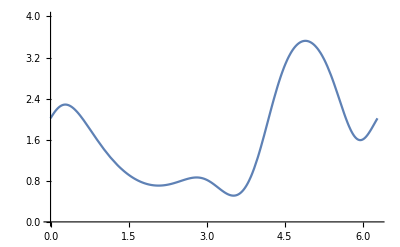

```mathematica
G[{η_,ξ1_,ξ2_},{b_}]:=FLORE[{η,ξ1,ξ2},{b}][g,Γ]
Plot[G[{η,0,0},{1}][[1]],{η,0,2π},PlotRange->{0,4}]
```

Finally, we rescale time and solve our BVP:

```mathematica
H[{η_,ξ1_,ξ2_},{b_}]:=Take[G[{η,ξ1,ξ2},{b}],{2,3}]/G[{η,ξ1,ξ2},{b}][[1]];
per=NDSolve[{
	{ξ1'[η],ξ2'[η]}==H[{η,ξ1[η],ξ2[η]},{1}],
	{ξ1[0],ξ2[0]}=={ξ1[2π],ξ2[2π]}},
	{ξ1,ξ2},
	{η,0,2π},
	Method->{"Shooting","StartingInitialConditions"->{ξ1[0]==0,ξ2[0]==0}}];
ParametricPlot3D[{η,ξ1[η],ξ2[η]}/.per,{η,0,2π},BoxRatios->{1, 1, 1},PlotPoints->100]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Flatten[(Γ[η]+ξ1[η]*N1Γ[η]+ξ2[η]*N2Γ[η])/.per],{η,0,2π}]
```

-Graphics3D-

We have found our periodic orbit, we can use the initial condition to find the trajectory

```mathematica
x0=Flatten[(Γ[0]+ξ1[0]*N1Γ[0]+ξ2[0]*N2Γ[0])/.per];
sol=NDSolve[{{x'[t],y'[t],z'[t]}==g[{x[t],y[t],z[t]},{1}],{x[0],y[0],z[0]}==x0},{x,y,z},{t,0,20}];
T=(t/.Quiet[FindRoot[(ν[{x[t],y[t],z[t]}-x0]/.sol)==0,{t,5,1,20}]]);
```

We first analyze the angular dynamics:

```mathematica
ϕ[t_]:=Flatten[{x[t],y[t],z[t]}/.sol];
FlowDerivative[vec_,vars_,pars_,order_]:=Module[{dummy},
dummy=Table[Subscript[𝓇,j],{j,1,Length[vars]}];
Nest[(D[#,{dummy}].vec[dummy,pars])&,vec[dummy,pars],order-1]/.Table[dummy[[j]]->vars[[j]],{j,1,Length[vars]}]];
Tϕ[t_]:=μ[g[ϕ[t],{1}]];
N1ϕ[t_]:=μ[#1-#1.#2*#2]&[FlowDerivative[g,ϕ[t],{1},2],Tϕ[t]];
N2ϕ[t_]:=Cross[Tϕ[t],N1ϕ[t]];
Ψϕ[{η_,ξ1_,ξ2_}]:=ϕ[η]+ξ1*N1ϕ[η]+ξ2*N2ϕ[η];
κ1ϕ[t_]:=Tϕ'[t].N1ϕ[t]/ν[g[ϕ[t],{1}]];
κ2ϕ[t_]:=N1ϕ'[t].N2ϕ[t]/ν[g[ϕ[t],{1}]];
gϕ[{η_,ξ1_,ξ2_},{λ_}]:=FLORE[{η,ξ1,ξ2},{1}][g,ϕ];
L[η_]:={{D[g[{α1,α2,α3},{1}],{{α1,α2,α3}}].#1.#1 , D[g[{α1,α2,α3},{1}],{{α1,α2,α3}}].#2.#1},{D[g[{α1,α2,α3},{1}],{{α1,α2,α3}}].#1.#2,D[g[{α1,α2,α3},{1}],{{α1,α2,α3}}].#2.#2}}&[N1ϕ[η],N2ϕ[η]]/.{α1->ϕ[η][[1]],α2->ϕ[η][[2]],α3->ϕ[η][[3]]};
R[η_,θ_]:=ν[g[ϕ[η],{1}]]*κ2ϕ[η]+Det[{{Cos[θ],Sin[θ]},L[η].{Cos[θ],Sin[θ]}}];
```

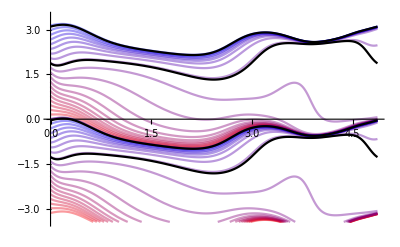

```mathematica
θsol=Parallelize[Table[
NDSolve[{θ'[η]==R[η,θ[η]],θ[0]==θ0},θ,{η,0,T},Method->{"EquationSimplification"->"Residual"}],{θ0,0,π,π/20}]];
θs=Flatten[Nest[(θ[T]/.NDSolve[{θ'[η]==R[η,θ[η]],θ[0]==#},θ,{η,0,T},Method->{"EquationSimplification"->"Residual"}])&,0,5]][[1]];
θu=Flatten[Nest[(θ[0]/.NDSolve[{θ'[η]==R[η,θ[η]],θ[T]==#},θ,{η,0,T},Method->{"EquationSimplification"->"Residual"}])&,0,5]][[1]];
stable=NDSolve[{θ'[η]==R[η,θ[η]],θ[0]==θs},θ,{η,0,T},Method->{"EquationSimplification"->"Residual"}];
unstable=NDSolve[{θ'[η]==R[η,θ[η]],θ[T]==θu},θ,{η,0,T},Method->{"EquationSimplification"->"Residual"}];
Show[Table[
Plot[θ[η]/.θsol[[i]],{η,0,T},PlotRange->{-π-.3,π+.3},PlotStyle->{Opacity[.4],Blend[{Red,Blue},i/Length[θsol]]}],{i,1,Length[θsol]}],
Table[
Plot[-π+θ[η]/.θsol[[i]],{η,0,T},PlotRange->{-π-.3,π+.3},PlotStyle->{Opacity[.4],Blend[{Red,Blue},i/Length[θsol]]}],{i,1,Length[θsol]}],
Plot[θ[η]/.stable,{η,0,T},PlotStyle->{Black}],
Plot[π+θ[η]/.stable,{η,0,T},PlotStyle->{Black}],
Plot[θ[η]/.unstable,{η,0,T},PlotStyle->{Black}],
Plot[-π+θ[η]/.unstable,{η,0,T},PlotStyle->{Black}]]
```

```mathematica
Show[Table[ParametricPlot3D[{η,Cos[θ[η]],Sin[θ[η]]}/.θsol[[i]],{η,0,T},BoxRatios->{T, 1, 1},PlotStyle->Blend[{Red,Blue},i/Length[θsol]],PlotRange->{{0,T},{-1,1},{-1,1}}],{i,1,Length[θsol]}],
Table[ParametricPlot3D[{η,Cos[θ[η]+π],Sin[θ[η]+π]}/.θsol[[i]],{η,0,T},BoxRatios->{1, 1, 1},PlotStyle->Blend[{Blue,Red},i/Length[θsol]],PlotRange->{{0,T},{-1,1},{-1,1}}],{i,1,Length[θsol]}]]
```

-Graphics3D-